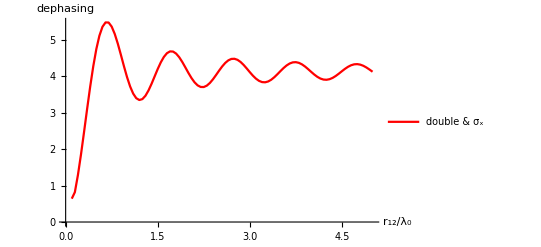

```mathematica
dphx=ListLinePlot[Table[{n,
k0=2Pi;θ=Pi/2;di=n λ0;Λ21=3/4(-(1-Cos[θ]^2)Cos[k0 di]/(k0 di)+(1-3 Cos[θ]^2)(Sin[k0 di]/(k0 di)^2+Cos[k0 di]/(k0 di)^3));γ12=3/2((1-Cos[θ]^2)Sin[k0 di]/(k0 di)+(1-3 Cos[θ]^2)(Cos[k0 di]/(k0 di)^2-Sin[k0 di]/(k0 di)^3));Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqx=NDSolve[{ρ'[t]==-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==initx,WhenEvent[Re[Evaluate[a[1,3][t]/.solsqx]+Evaluate[a[2,4][t]/.solsqx]+Evaluate[a[3,1][t]/.solsqx]+Evaluate[a[4,2][t]/.solsqx]][[1]]==1/E,dx=1/t]},slnn,{t,0,10},MaxSteps->1000000];dx},{n,0.1,5,0.05}],AxesLabel->{"r_12/λ_0","dephasing"},PlotStyle->Red,PlotLegends->LineLegend[{"double & σ_x"}],PlotRange->All]
```

```mathematica
dphy=ListLinePlot[Table[{n,
di=n λ0;Λ21=3/4 γ(-(1-Cos[θ]^2)Cos[k0 di]/(k0 di)+(1-3 Cos[θ]^2)(Sin[k0 di]/(k0 di)^2+Cos[k0 di]/(k0 di)^3));γ12=3/2((1-Cos[θ]^2)Sin[k0 di]/(k0 di)+(1-3 Cos[θ]^2)(Cos[k0 di]/(k0 di)^2-Sin[k0 di]/(k0 di)^3));Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqy=NDSolve[{ρ'[t]==-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==inity,WhenEvent[Im[-Evaluate[a[1,3][t]/.solsqy]-Evaluate[a[2,4][t]/.solsqy]+Evaluate[a[3,1][t]/.solsqy]+Evaluate[a[4,2][t]/.solsqy]][[1]]==1/E,dy=1/t]},slnn,{t,0,10},MaxSteps->50000000];dy},{n,0.1,5,0.05}],AxesLabel->{"r_12/λ_0","dephasing"},PlotLegends->LineLegend[{"double & σ_y"}],PlotRange->All,PlotStyle->Red]
```

NDSolve::nbnum1: The function value … is not True or False when the arguments are {0.,0.25+0. ⅈ,0.-0.25 ⅈ,0.-0.25 ⅈ,-0.25+0. ⅈ,0.+0.25 ⅈ,0.25+0. ⅈ,0.25+0. ⅈ,0.-0.25 ⅈ,0.+0.25 ⅈ,0.25+0. ⅈ,«12»,-0.656859+0. ⅈ,-0.649273-0.0369077 ⅈ,0.649273-0.693766 ⅈ,-0.656859+0. ⅈ,-0.649749+0. ⅈ,-0.649273-0.0369077 ⅈ,0.656859+0. ⅈ,-0.649273+0.0369077 ⅈ,-0.649273+0.0369077 ⅈ,1.38042+0. ⅈ}.

NDSolve::nbnum1: The function value … is not True or False when the arguments are {0.0000733111,0.249994+0. ⅈ,0.0000475838-0.249949 ⅈ,0.0000475838-0.249949 ⅈ,-0.249952+0. ⅈ,0.0000475838+0.249949 ⅈ,0.249952+0. ⅈ,«19»,-0.656646+0. ⅈ,-0.649531+0. ⅈ,-0.649162-0.0366222 ⅈ,0.65662+0. ⅈ,-0.649162+0.0366222 ⅈ,-0.649162+0.0366222 ⅈ,1.38008+0. ⅈ}.

NDSolve::nbnum1: The function value … is not True or False when the arguments are {0.000146622,0.249988+0. ⅈ,0.0000951525-0.249898 ⅈ,0.0000951525-0.249898 ⅈ,-0.249904+0. ⅈ,0.0000951525+0.249898 ⅈ,0.249905+0. ⅈ,«19»,-0.656434+0. ⅈ,-0.649312+0. ⅈ,-0.649051-0.0363367 ⅈ,0.656382+0. ⅈ,-0.649051+0.0363367 ⅈ,-0.649051+0.0363367 ⅈ,1.37973+0. ⅈ}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

-Graphics-

```mathematica
sx=Plot[-1/2(-1-2sh^2+2ch sh 3/2((1-Cos[θ]^2)Sin[k0 n]/(k0 n)+(1-3 Cos[θ]^2)(Cos[k0 n]/(k0 n)^2-Sin[k0 n]/(k0 n)^3))),{n,0,5}];
sy=Plot[-1/2(-ch^2-sh^2-Sinh[2 rr] 3/2((1-Cos[θ]^2)Sin[k0 n]/(k0 n)+(1-3 Cos[θ]^2)(Cos[k0 n]/(k0 n)^2-Sin[k0 n]/(k0 n)^3))),{n,0,5}];
```

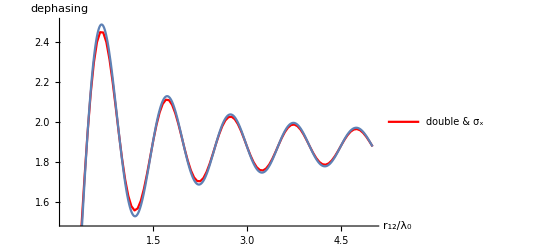

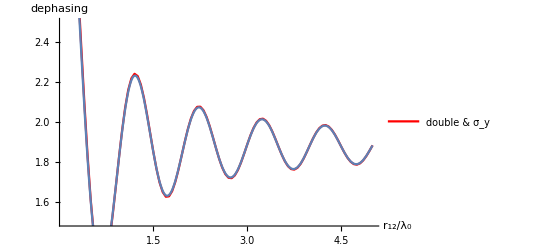

```mathematica
Show[{dphx,sx},PlotRange->{1.5,2.5}] (*r=1*)
Show[{dphy,sy},PlotRange->{1.5,2.5}] (*r=1*)
```

```mathematica
ρs[t_]:=Table[s[i,j][t],{i,2},{j,2}];σps=({{0, 1}, {0, 0}});σms=({{0, 0}, {1, 0}});
```

```mathematica
Tr[(σps+σms).(sh ch f(σps.ρs[t].σps+σms.ρs[t].σms)-1/2(sh^2+1)(ρs[t].σps.σms+σps.σms.ρs[t]-2σms.ρs[t].σps)-1/2 sh^2(ρs[t].σms.σps+σms.σps.ρs[t]-2σps.ρs[t].σms ))]
```

ch f sh s[1,2][t]-1/2 sh^2 s[1,2][t]-1/2 (1+sh^2) s[1,2][t]+ch f sh s[2,1][t]-1/2 sh^2 s[2,1][t]-1/2 (1+sh^2) s[2,1][t]

```mathematica
Simplify[ch f sh s[1,2][t]-1/2 sh^2 s[1,2][t]-1/2 (1+sh^2) s[1,2][t]+ch f sh s[2,1][t]-1/2 sh^2 s[2,1][t]-1/2 (1+sh^2) s[2,1][t]]
```

1/2 (-1+2 ch f sh-2 sh^2) (s[1,2][t]+s[2,1][t])